```mathematica
√(x^2+y^2)
```

√(x^2+y^2)

```mathematica
thething = Sum[ⅇ^(d/40)BesselJ[0,√((x-d-30)^2+y^2)],{d,-100,0,0.4}]/60;
```

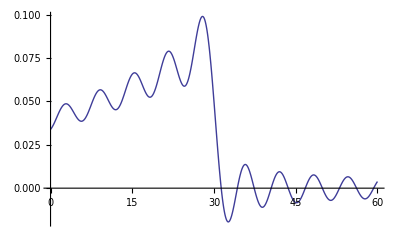

```mathematica
Plot[ Sum[ⅇ^(d/40)BesselJ[0,√((x-d-30)^2)],{d,-100,0,0.4}]/60,{x,0,60}]
```

```mathematica
expdp = DensityPlot[thething,{x,0,60},{y,-30,30},PlotPoints->{100,100},PlotLegends->BarLegend[Automatic,LegendLabel->"ζ (mm)",LabelStyle->{FontFamily->"Times",FontSize->18}],PlotRange->All, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->18}, FrameLabel->{Row[{Style["x",FontSlant->Italic]," (mm)"}],Row[{Style["y",FontSlant->Italic]," (mm)"}]},RotateLabel->True]
```

-Graphics-

```mathematica
Export["/Users/cricha5/Desktop/Physics/HydroAnalogsGit/Graphics/WaveFront3D.png",expdp]
```

/Users/cricha5/Desktop/Physics/HydroAnalogsGit/Graphics/WaveFront3D.png

```mathematica
ⅈ k (N-n) dr rrr Sin[ϕ]-(N-n)/M
```

-(-n+N)/M+ⅈ dr k (-n+N) rrr Sin[ϕ]

```mathematica
ⅈ k N dr rrr Sin[ϕ]-ⅈ k n dr rrr Sin[ϕ]-N/M+n/M
```

n/M-N/M-ⅈ dr k n rrr Sin[ϕ]+ⅈ dr k N rrr Sin[ϕ]

```mathematica
ⅇ^(-N/M+ⅈ dr k N rrr Sin[ϕ])
```

ⅇ^(-N/M+ⅈ dr k N rrr Sin[ϕ])

```mathematica
ⅇ^(n/M-ⅈ dr k n rrr Sin[ϕ])
```

ⅇ^(n/M-ⅈ dr k n rrr Sin[ϕ])

```mathematica
ⅇ^(-N/M+ⅈ dr k N rrr Sin[ϕ])ⅇ^(n/M-ⅈ dr k n rrr Sin[ϕ])
```

```mathematica
ⅇ^((1/M-ⅈ dr k  rrr Sin[ϕ])n)
```

ⅇ^(n (1/M-ⅈ dr k rrr Sin[ϕ]))

```mathematica
ⅇ^((n+1) (1/M-ⅈ dr k rrr Sin[ϕ]))
```

```mathematica
ⅇ^(1/M-ⅈ dr k rrr Sin[ϕ])ⅇ^(-NN/M+ⅈ dr k NN rrr Sin[ϕ])(1-ⅇ^(NN(1/M-ⅈ dr k rrr Sin[ϕ])))/(1-ⅇ^(1/M-ⅈ dr k rrr Sin[ϕ]))
```

(ⅇ^(1/M-NN/M-ⅈ dr k rrr Sin[ϕ]+ⅈ dr k NN rrr Sin[ϕ]) (1-ⅇ^(NN (1/M-ⅈ dr k rrr Sin[ϕ]))))/(1-ⅇ^(1/M-ⅈ dr k rrr Sin[ϕ]))

```mathematica
FullSimplify[(ⅇ^(1/M-NN/M-ⅈ dr k rrr Sin[ϕ]+ⅈ dr k NN rrr Sin[ϕ]) (1-ⅇ^(NN (1/M-ⅈ dr k rrr Sin[ϕ]))))/(1-ⅇ^(1/M-ⅈ dr k rrr Sin[ϕ]))]
```

```mathematica
(1-ⅇ^(-NN/M+ⅈ dr k NN rrr Sin[ϕ]))/(1-ⅇ^(ⅈ dr k rrr Sin[ϕ]-1/M))
```

(1-ⅇ^(-NN/M+ⅈ dr k NN rrr Sin[ϕ]))/(1-ⅇ^(-1/M+ⅈ dr k rrr Sin[ϕ]))